## Parámetros comunes

```mathematica
ColoresTema=ColorData[106,"ColorList"];
```

## Gráficas del Registro (log)

```mathematica
Folder="C:\\Users\\Rodrigo\\Desktop\\Tesis\\DAQ\\Datos_Para_Entrenamiento\\Logs\\";
SetDirectory[Folder];
Run["dir /b > filename.txt"];
Files=Import["filename.txt","List"];
GenVsSet={{"File","Total Generations"}};
```

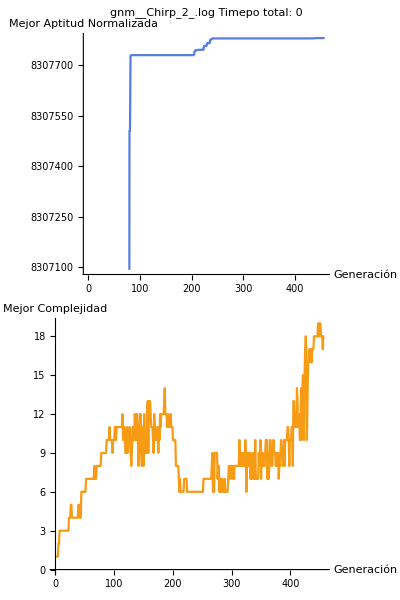

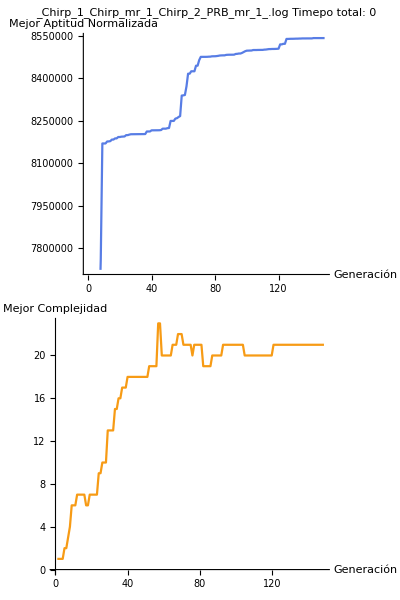

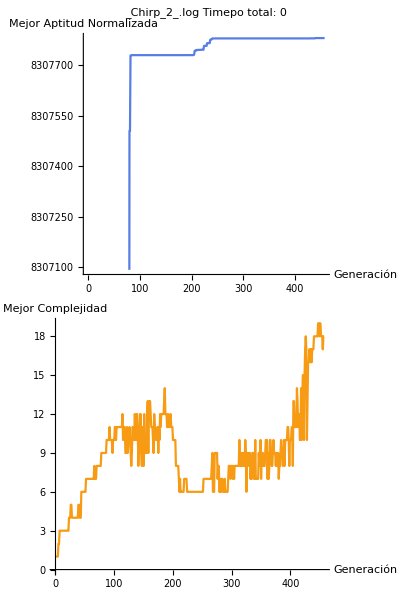

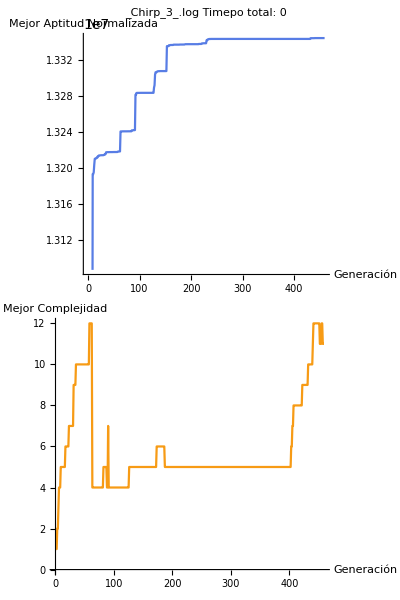

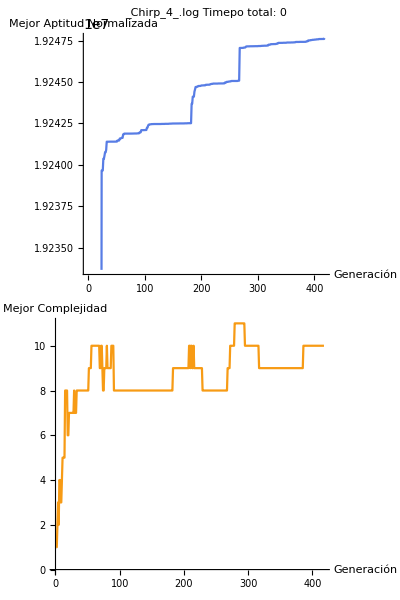

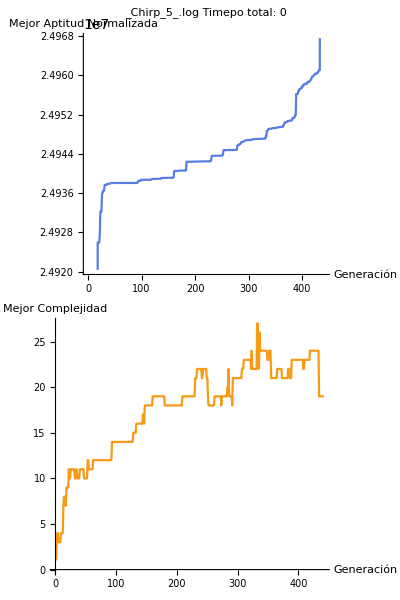

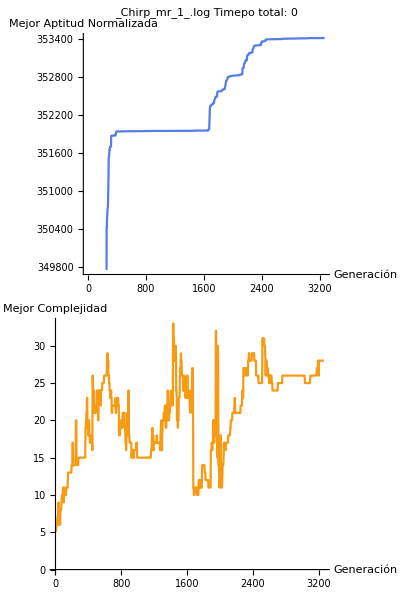

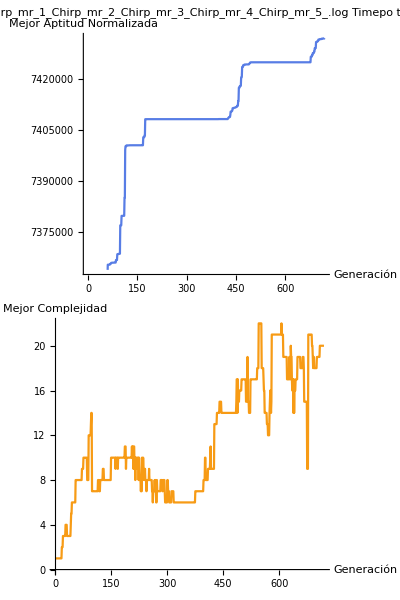

```mathematica
For[i=3,i<=Length[Files],i++,
If[StringCount[Files[[i]],".log"]>0,
Data=Import[Files[[i]],"Data"];
GenVsSet=Join[GenVsSet,{{Files[[i]],Data[[-2,2]]}}];
TotalT=DateObject[Data[[-2,1]]]-DateObject[Data[[2,1]]];
TotalT=ToString[UnitConvert[TotalT,MixedRadix["Hours","Minutes","Seconds"]],StandardForm];
Imagen=ListLinePlot[Data[[2;;-2,2;;3]],
ImagePadding->60,
ImageSize->Medium,
PlotStyle->ColoresTema[[1]],
AxesLabel->{"Generación","Mejor Aptitud Normalizada"},
PlotLabel->Files[[i]]<>" 
Timepo total: " <>TotalT];
Imagen2=ListLinePlot[Data[[2;;-2,2;;6;;4]],
ImagePadding->60,
ImageSize->Medium,
PlotStyle->ColoresTema[[2]],
AxesLabel->{"Generación","Mejor Complejidad"}
];
Img=Grid[{{Imagen},{Imagen2}}];
Print[Img]
(*Export[Folder<>"Graficas\\"<>"Grafica_"<>Files[[i]]<>".eps",Imagen]*)
]
]
```

## Pruebas

{ Chirp_1.csv,Chirp_2.csv,Chirp_3.csv,Chirp_4.csv,Chirp_5.csv,Chirp_mr_1.csv,Chirp_mr_2.csv,Chirp_mr_3.csv,Chirp_mr_4.csv,Chirp_mr_5.csv,22/11/2019  03:04 p. m.            42,358 Impulso_1.csv,13/12/2019  12:19 p. m.           179,162 Plot_CSV_1.nb,22/11/2019  02:55 p. m.           411,521 PRB1.csv,22/11/2019  02:55 p. m.           412,551 PRB2.csv,22/11/2019  02:56 p. m.           412,569 PRB3.csv,22/11/2019  02:56 p. m.           412,719 PRB4.csv,22/11/2019  02:56 p. m.           412,740 PRB5.csv,22/11/2019  02:57 p. m.           402,097 PRB_1.csv,22/11/2019  02:57 p. m.           400,646 PRB_2.csv,22/11/2019  02:57 p. m.           400,640 PRB_3.csv,22/11/2019  02:58 p. m.           400,400 PRB_4.csv,22/11/2019  02:58 p. m.           400,566 PRB_5.csv,22/11/2019  03:12 p. m.            40,225 PRB_mr_51.csv,22/11/2019  03:12 p. m.            40,207 PRB_mr_52.csv}

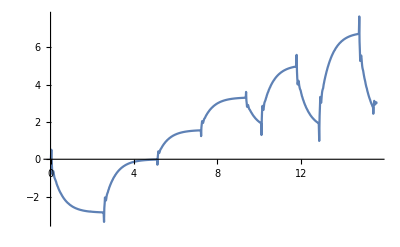

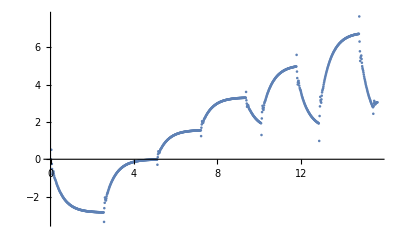

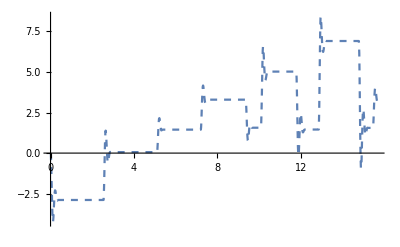

InterpolatingFunction::dmval: Input value {0.000194071} lies outside the range of data in the interpolating function. Extrapolation will be used.

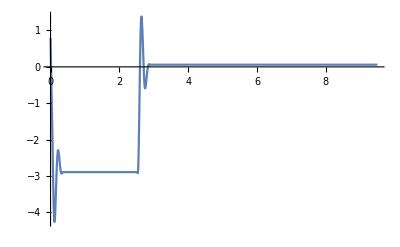

InterpolatingFunction::dmval: Input value {0.000194071} lies outside the range of data in the interpolating function. Extrapolation will be used.

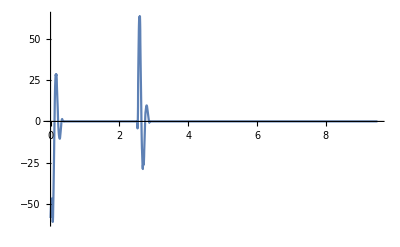

```mathematica
Data=Import["C:\\Users\\Rodrigo\\Desktop\\Tesis\\DAQ\\Datos_Para_Entrenamiento\\GenomasGanadores\\ValidationControlnMotorReaction.csv","Data"];
ListLinePlot[Data[[1;;1000,1;;2]]]
ListPlot[Data[[1;;1000,1;;2]]]
ListLinePlot[Data[[1;;1000,1;;3;;2]],PlotStyle->Dashed]
IntPos=Interpolation[Data[[1;;200,1;;3;;2]]];
DIntPos=D[IntPos[t],t];
Plot[IntPos[t],{t,0,9.5}]
Plot[DIntPos,{t,0,9.5}]
```

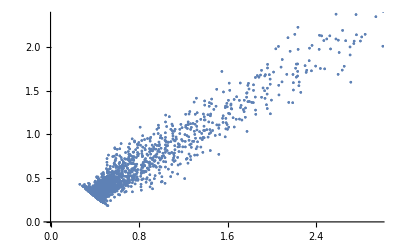

```mathematica
ListPlot[Abs[Fourier[Data[[;;,1;;2]]]]]
```

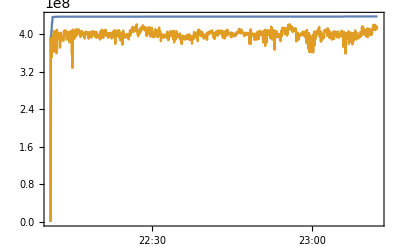

```mathematica
DateListPlot[{Data[[2;;,1;;3;;2]],Data[[2;;,1;;4;;3]]}]
Data[[2;;,1]]
```

```mathematica
((TimeObject[Data[[Length[Data],1]]]-Evaluate[TimeObject[Data[[2,1]]]])<<QuantityUnitsLoader`)/Null
```

1.02121 h

```mathematica
-TimeObject["2019-12-29 22:11:00.456"]+TimeObject["2019-12-29 22:11:02.610"]
```

QuantityUnits`Private`ToQuantity[QuantityUnits`Private`UnknownQuantity[2.154,Seconds]]

QuantityUnits`Private`ToQuantity[QuantityUnits`Private`UnknownQuantity[1.60145,Days]]

```mathematica
RebuildPacletData[]
```

Null^2

```mathematica
%229
```

1.02121 h

```mathematica
ListLinePlot[Data[[2;;,2;;3]],AxesLabel->{"Generación","Mejor Aptitud"},PlotLabel->Files[[i]]<>" Timepo total " <>TotalT]
```

```mathematica
TotalT
```

1.02121 hours

```mathematica
DateObject[Data[[Length[Data],1]]]-DateObject[Data[[2,1]]]
```

1.02121 h

```mathematica
UnitConvert[Quantity[1.0212086111969416,"Hours"],MixedRadix["Hours","Minutes","Seconds"]]
```

1 1

```mathematica
UnitConvert[Quantity[1.0212086111969416,"Hours"],MixedRadix["Hours","Minutes","Seconds"]]
```

1 1

```mathematica
Simplify[Null Quantity[1.0212086111969416,"Hours"]]
```

Null (1.02121 h)

```mathematica
UnitConvert[Quantity[1.0212086111969416,"Hours"],MixedRadix["Hours","Minutes","Seconds"]]
```

1 1

```mathematica
Data[[1,1]]
```

ClockTime

```mathematica
-
```

```mathematica
ColoresTema[[1;;2]]
```

{Hue[0.6, 0.7, 0.8],Hue[0.22, 1, 0.7]}

```mathematica
Data[[1;;-2,2;;3]]//MatrixForm
```

(0 | 0
1 | 2.65352×10^7
2 | 2.65352×10^7
3 | 2.65352×10^7
4 | 2.65352×10^7
5 | 2.65352×10^7
6 | 2.65352×10^7
7 | 2.65352×10^7
8 | 2.65352×10^7
9 | 2.7539×10^7
10 | 2.7539×10^7
11 | 2.78512×10^7
12 | 2.97903×10^7
13 | 2.97903×10^7
14 | 2.99009×10^7
15 | 3.13494×10^7
16 | 3.13497×10^7
17 | 3.13498×10^7
18 | 3.13499×10^7
19 | 3.13499×10^7
20 | 3.13499×10^7
21 | 3.13499×10^7
22 | 3.13623×10^7
23 | 3.13627×10^7
24 | 3.13652×10^7
25 | 3.13657×10^7
26 | 3.13663×10^7
27 | 3.13709×10^7
28 | 3.14181×10^7
29 | 3.14181×10^7
30 | 3.14189×10^7
31 | 3.14189×10^7
32 | 3.14189×10^7
33 | 3.14192×10^7
34 | 3.142×10^7
35 | 3.14203×10^7
36 | 3.14208×10^7
37 | 3.1421×10^7
38 | 3.14211×10^7
39 | 3.14211×10^7
40 | 3.14211×10^7
41 | 3.14211×10^7
42 | 3.14211×10^7
43 | 3.14211×10^7
44 | 3.14211×10^7
45 | 3.14211×10^7
46 | 3.14212×10^7
47 | 3.14214×10^7
48 | 3.14214×10^7
49 | 3.14221×10^7
50 | 3.14222×10^7
51 | 3.14222×10^7
52 | 3.14222×10^7
53 | 3.14223×10^7
54 | 3.14223×10^7
55 | 3.14223×10^7
56 | 3.14224×10^7
57 | 3.1449×10^7
58 | 3.1449×10^7
59 | 3.14491×10^7
60 | 3.14501×10^7
61 | 3.14501×10^7
62 | 3.14501×10^7
63 | 3.14501×10^7
64 | 3.14503×10^7
65 | 3.14503×10^7
66 | 3.14503×10^7
67 | 3.14503×10^7
68 | 3.14503×10^7
69 | 3.14503×10^7
70 | 3.14503×10^7
71 | 3.14503×10^7
72 | 3.14503×10^7
73 | 3.14506×10^7
74 | 3.14506×10^7
75 | 3.14506×10^7
76 | 3.14506×10^7
77 | 3.14506×10^7
78 | 3.14507×10^7
79 | 3.14509×10^7
80 | 3.14509×10^7
81 | 3.14511×10^7
82 | 3.14513×10^7
83 | 3.14513×10^7
84 | 3.14514×10^7
85 | 3.14514×10^7
86 | 3.14516×10^7
87 | 3.14516×10^7
88 | 3.14516×10^7
89 | 3.14516×10^7
90 | 3.14518×10^7
91 | 3.1452×10^7
92 | 3.14522×10^7
93 | 3.14522×10^7
94 | 3.14525×10^7
95 | 3.14525×10^7
96 | 3.14525×10^7
97 | 3.14527×10^7
98 | 3.14527×10^7
99 | 3.14531×10^7
100 | 3.14537×10^7
101 | 3.14537×10^7
102 | 3.14537×10^7
103 | 3.14537×10^7
104 | 3.14538×10^7
105 | 3.14538×10^7
106 | 3.14538×10^7
107 | 3.14539×10^7
108 | 3.14539×10^7
109 | 3.14539×10^7
110 | 3.14541×10^7
111 | 3.14541×10^7
112 | 3.14541×10^7
113 | 3.14541×10^7
114 | 3.14542×10^7
115 | 3.14546×10^7
116 | 3.14546×10^7
117 | 3.14546×10^7
118 | 3.14546×10^7
119 | 3.14546×10^7
120 | 3.14547×10^7
121 | 3.14547×10^7
122 | 3.14613×10^7
123 | 3.14613×10^7
124 | 3.14613×10^7
125 | 3.14613×10^7
126 | 3.14654×10^7
127 | 3.14665×10^7
128 | 3.14665×10^7
129 | 3.14696×10^7
130 | 3.14696×10^7
131 | 3.14711×10^7
132 | 3.14711×10^7
133 | 3.14719×10^7
134 | 3.14719×10^7
135 | 3.14721×10^7
136 | 3.14723×10^7
137 | 3.14728×10^7
138 | 3.14728×10^7
139 | 3.14733×10^7
140 | 3.14733×10^7
141 | 3.14733×10^7
142 | 3.14733×10^7
143 | 3.14737×10^7
144 | 3.14737×10^7
145 | 3.14737×10^7
146 | 3.14737×10^7
147 | 3.14739×10^7
148 | 3.14739×10^7
149 | 3.14739×10^7
150 | 3.1474×10^7
151 | 3.14743×10^7
152 | 3.14743×10^7
153 | 3.14743×10^7
154 | 3.14745×10^7
155 | 3.14748×10^7
156 | 3.14748×10^7
157 | 3.14749×10^7
158 | 3.14749×10^7
159 | 3.14749×10^7
160 | 3.14751×10^7
161 | 3.14751×10^7
162 | 3.14751×10^7
163 | 3.14752×10^7
164 | 3.14753×10^7
165 | 3.14753×10^7
166 | 3.14753×10^7
167 | 3.14756×10^7
168 | 3.14756×10^7
169 | 3.14756×10^7
170 | 3.14772×10^7
171 | 3.14772×10^7
172 | 3.14778×10^7
173 | 3.14778×10^7
174 | 3.14778×10^7
175 | 3.14779×10^7
176 | 3.14779×10^7
177 | 3.1478×10^7
178 | 3.14781×10^7
179 | 3.14781×10^7
180 | 3.14782×10^7
181 | 3.14782×10^7
182 | 3.14783×10^7
183 | 3.14783×10^7
184 | 3.14786×10^7
185 | 3.14786×10^7
186 | 3.14786×10^7
187 | 3.14787×10^7
188 | 3.14787×10^7
189 | 3.14788×10^7
190 | 3.14788×10^7
191 | 3.14788×10^7
192 | 3.14788×10^7
193 | 3.14788×10^7
194 | 3.14788×10^7
195 | 3.14788×10^7
196 | 3.1479×10^7
197 | 3.1479×10^7
198 | 3.14792×10^7
199 | 3.14792×10^7
200 | 3.14793×10^7
201 | 3.14793×10^7
202 | 3.14793×10^7
203 | 3.14793×10^7
204 | 3.14794×10^7
205 | 3.14794×10^7
206 | 3.14796×10^7
207 | 3.14796×10^7
208 | 3.14796×10^7
209 | 3.14796×10^7
210 | 3.14796×10^7
211 | 3.14796×10^7
212 | 3.14796×10^7
213 | 3.14796×10^7
214 | 3.14796×10^7
215 | 3.14797×10^7
216 | 3.14797×10^7
217 | 3.14797×10^7
218 | 3.14797×10^7
219 | 3.14797×10^7
220 | 3.14797×10^7
221 | 3.14797×10^7
222 | 3.14797×10^7
223 | 3.14798×10^7
224 | 3.14798×10^7
225 | 3.14798×10^7
226 | 3.14798×10^7
227 | 3.14798×10^7
228 | 3.14798×10^7
229 | 3.14798×10^7
230 | 3.14798×10^7
231 | 3.14798×10^7
232 | 3.14798×10^7
233 | 3.14798×10^7
234 | 3.14798×10^7
235 | 3.14798×10^7
236 | 3.14798×10^7
237 | 3.14798×10^7
238 | 3.14798×10^7
239 | 3.14798×10^7
240 | 3.14798×10^7
241 | 3.14799×10^7
242 | 3.148×10^7
243 | 3.148×10^7
244 | 3.148×10^7
245 | 3.148×10^7
246 | 3.148×10^7
247 | 3.148×10^7
248 | 3.14817×10^7
249 | 3.14817×10^7
250 | 3.14817×10^7
251 | 3.14826×10^7
252 | 3.14826×10^7
253 | 3.14826×10^7
254 | 3.14829×10^7
255 | 3.14829×10^7
256 | 3.14829×10^7
257 | 3.1483×10^7
258 | 3.1483×10^7
259 | 3.1483×10^7
260 | 3.1483×10^7
261 | 3.1483×10^7
262 | 3.1483×10^7
263 | 3.1483×10^7
264 | 3.1483×10^7
265 | 3.1483×10^7
266 | 3.1483×10^7
267 | 3.1483×10^7
268 | 3.1483×10^7
269 | 3.1483×10^7
270 | 3.1483×10^7
271 | 3.1483×10^7
272 | 3.1483×10^7
273 | 3.1483×10^7
274 | 3.1483×10^7
275 | 3.1483×10^7
276 | 3.1483×10^7
277 | 3.1483×10^7
278 | 3.1483×10^7
279 | 3.1483×10^7
280 | 3.1483×10^7
281 | 3.1483×10^7
282 | 3.1483×10^7
283 | 3.1483×10^7
284 | 3.1483×10^7
285 | 3.1483×10^7
286 | 3.1483×10^7
287 | 3.1483×10^7
288 | 3.1483×10^7
289 | 3.1483×10^7
290 | 3.1483×10^7
291 | 3.14831×10^7
292 | 3.14831×10^7
293 | 3.14831×10^7
294 | 3.14831×10^7
295 | 3.14831×10^7
296 | 3.14831×10^7
297 | 3.14831×10^7
298 | 3.14831×10^7
299 | 3.14831×10^7
300 | 3.14831×10^7
301 | 3.14831×10^7
302 | 3.14831×10^7
303 | 3.14831×10^7
304 | 3.14831×10^7
305 | 3.14833×10^7
306 | 3.14833×10^7
307 | 3.14833×10^7
308 | 3.14833×10^7
309 | 3.14833×10^7
310 | 3.14833×10^7
311 | 3.14833×10^7
312 | 3.14833×10^7
313 | 3.14833×10^7
314 | 3.14833×10^7
315 | 3.14833×10^7
316 | 3.14833×10^7
317 | 3.14833×10^7
318 | 3.14833×10^7
319 | 3.14833×10^7
320 | 3.14833×10^7
321 | 3.14833×10^7
322 | 3.14833×10^7
323 | 3.14833×10^7
324 | 3.14833×10^7
325 | 3.14833×10^7
326 | 3.14833×10^7
327 | 3.14833×10^7
328 | 3.14833×10^7
329 | 3.14833×10^7
330 | 3.14833×10^7
331 | 3.14833×10^7
332 | 3.14833×10^7
333 | 3.14833×10^7
334 | 3.14833×10^7
335 | 3.14833×10^7
336 | 3.14833×10^7
337 | 3.14833×10^7
338 | 3.14833×10^7
339 | 3.14833×10^7
340 | 3.14833×10^7
341 | 3.14833×10^7
342 | 3.14833×10^7
343 | 3.14833×10^7
344 | 3.14833×10^7
345 | 3.14833×10^7
346 | 3.14833×10^7
347 | 3.14833×10^7
348 | 3.14833×10^7
349 | 3.14833×10^7
350 | 3.14833×10^7
351 | 3.14833×10^7
352 | 3.14833×10^7
353 | 3.14833×10^7
354 | 3.14833×10^7
355 | 3.14833×10^7
356 | 3.14833×10^7
357 | 3.14833×10^7
358 | 3.14833×10^7
359 | 3.14833×10^7
360 | 3.14833×10^7
361 | 3.14833×10^7
362 | 3.14833×10^7
363 | 3.14833×10^7
364 | 3.14833×10^7
365 | 3.14833×10^7
366 | 3.14833×10^7
367 | 3.14833×10^7
368 | 3.14833×10^7
369 | 3.14833×10^7
370 | 3.14833×10^7
371 | 3.14833×10^7
372 | 3.14833×10^7
373 | 3.14833×10^7
374 | 3.14833×10^7
375 | 3.14833×10^7
376 | 3.14833×10^7
377 | 3.14833×10^7
378 | 3.14833×10^7
379 | 3.14833×10^7
380 | 3.14833×10^7
381 | 3.14833×10^7
382 | 3.14833×10^7
383 | 3.14833×10^7
384 | 3.14833×10^7
385 | 3.14833×10^7
386 | 3.14833×10^7
387 | 3.14833×10^7
388 | 3.14833×10^7
389 | 3.14833×10^7
390 | 3.14833×10^7
391 | 3.14833×10^7
392 | 3.14833×10^7
393 | 3.14833×10^7
394 | 3.14833×10^7
395 | 3.14833×10^7
396 | 3.14833×10^7
397 | 3.14833×10^7
398 | 3.14833×10^7
399 | 3.14833×10^7
400 | 3.14833×10^7
401 | 3.14833×10^7
402 | 3.14833×10^7
403 | 3.14833×10^7
404 | 3.14834×10^7
405 | 3.14834×10^7
406 | 3.14834×10^7
407 | 3.14834×10^7
408 | 3.14834×10^7
409 | 3.14834×10^7
410 | 3.14834×10^7
411 | 3.14834×10^7
412 | 3.14834×10^7
413 | 3.14834×10^7
414 | 3.14834×10^7
415 | 3.14834×10^7
416 | 3.14834×10^7
417 | 3.14834×10^7
418 | 3.14834×10^7
419 | 3.15166×10^7
420 | 3.15494×10^7
421 | 3.15566×10^7
422 | 3.16349×10^7
423 | 3.16929×10^7
424 | 3.16929×10^7
425 | 3.16929×10^7
426 | 3.17313×10^7
427 | 3.17313×10^7
428 | 3.17313×10^7
429 | 3.17313×10^7
430 | 3.17322×10^7
431 | 3.17322×10^7
432 | 3.17322×10^7
433 | 3.17571×10^7
434 | 3.1765×10^7
435 | 3.1765×10^7
436 | 3.1765×10^7
437 | 3.17652×10^7
438 | 3.17652×10^7
439 | 3.17652×10^7
440 | 3.17653×10^7
441 | 3.17661×10^7
442 | 3.17661×10^7
443 | 3.17671×10^7
444 | 3.17671×10^7
445 | 3.17671×10^7
446 | 3.17671×10^7
447 | 3.17671×10^7
448 | 3.17671×10^7
449 | 3.17671×10^7
450 | 3.17672×10^7
451 | 3.17672×10^7
452 | 3.17672×10^7
453 | 3.17672×10^7
454 | 3.17672×10^7
455 | 3.17672×10^7
456 | 3.17673×10^7
457 | 3.17673×10^7
458 | 3.17673×10^7
459 | 3.17673×10^7
460 | 3.17673×10^7
461 | 3.17673×10^7
462 | 3.17695×10^7
463 | 3.177×10^7
464 | 3.177×10^7
465 | 3.17704×10^7
466 | 3.17704×10^7
467 | 3.17704×10^7
468 | 3.17704×10^7
469 | 3.17704×10^7
470 | 3.17805×10^7
471 | 3.17805×10^7
472 | 3.17805×10^7
473 | 3.17805×10^7
474 | 3.17805×10^7
475 | 3.17813×10^7
476 | 3.18891×10^7
477 | 3.18891×10^7
478 | 3.19302×10^7
479 | 3.19302×10^7
480 | 3.20056×10^7
481 | 3.20056×10^7
482 | 3.21612×10^7
483 | 3.21612×10^7
484 | 3.21695×10^7
485 | 3.21695×10^7
486 | 3.21955×10^7
487 | 3.22239×10^7
488 | 3.22241×10^7
489 | 3.22241×10^7
490 | 3.22241×10^7
491 | 3.22243×10^7
492 | 3.22243×10^7
493 | 3.22244×10^7
494 | 3.22244×10^7
495 | 3.22244×10^7
496 | 3.22244×10^7
497 | 3.22433×10^7
498 | 3.22433×10^7
499 | 3.22697×10^7
500 | 3.22697×10^7
501 | 3.22697×10^7
502 | 3.22698×10^7
503 | 3.22705×10^7
504 | 3.2271×10^7
505 | 3.2271×10^7
506 | 3.2271×10^7
507 | 3.2271×10^7
508 | 3.2271×10^7
509 | 3.2271×10^7
510 | 3.2271×10^7
511 | 3.22712×10^7
512 | 3.22712×10^7
513 | 3.22712×10^7
514 | 3.22732×10^7
515 | 3.22732×10^7
516 | 3.22732×10^7
517 | 3.22732×10^7
518 | 3.22736×10^7
519 | 3.22737×10^7
520 | 3.22737×10^7
521 | 3.22737×10^7
522 | 3.22737×10^7
523 | 3.22737×10^7
524 | 3.22737×10^7
525 | 3.22737×10^7
526 | 3.22737×10^7
527 | 3.22737×10^7
528 | 3.22737×10^7
529 | 3.22737×10^7
530 | 3.22738×10^7
531 | 3.22738×10^7
532 | 3.22738×10^7
533 | 3.22738×10^7
534 | 3.22755×10^7
535 | 3.22755×10^7
536 | 3.22792×10^7
537 | 3.22881×10^7
538 | 3.22913×10^7
539 | 3.22913×10^7
540 | 3.22913×10^7
541 | 3.22913×10^7
542 | 3.22913×10^7
543 | 3.22913×10^7
544 | 3.22916×10^7
545 | 3.22916×10^7
546 | 3.22916×10^7
547 | 3.22916×10^7
548 | 3.22917×10^7
549 | 3.22917×10^7
550 | 3.22917×10^7
551 | 3.22933×10^7
552 | 3.22933×10^7
553 | 3.22933×10^7
554 | 3.22933×10^7
555 | 3.22933×10^7
556 | 3.22935×10^7
557 | 3.22936×10^7
558 | 3.22936×10^7
559 | 3.22937×10^7
560 | 3.22937×10^7
561 | 3.22937×10^7
562 | 3.22937×10^7
563 | 3.22937×10^7
564 | 3.22937×10^7
565 | 3.22937×10^7
566 | 3.22937×10^7
567 | 3.22937×10^7
568 | 3.22937×10^7
569 | 3.22937×10^7
570 | 3.22937×10^7
571 | 3.22937×10^7
572 | 3.22937×10^7
573 | 3.22937×10^7
574 | 3.22937×10^7
575 | 3.22937×10^7
576 | 3.22937×10^7
577 | 3.22937×10^7
578 | 3.22951×10^7
579 | 3.22951×10^7
580 | 3.22951×10^7
581 | 3.22981×10^7
582 | 3.22981×10^7
583 | 3.22981×10^7
584 | 3.22981×10^7
585 | 3.22988×10^7
586 | 3.22988×10^7
587 | 3.22988×10^7
588 | 3.22988×10^7
589 | 3.22988×10^7
590 | 3.22988×10^7
591 | 3.22988×10^7
592 | 3.22988×10^7
593 | 3.22988×10^7
594 | 3.2299×10^7
595 | 3.2299×10^7
596 | 3.2299×10^7
597 | 3.2299×10^7
598 | 3.2299×10^7
599 | 3.2299×10^7
600 | 3.2299×10^7
601 | 3.2299×10^7
602 | 3.2299×10^7
603 | 3.2299×10^7
604 | 3.22991×10^7
605 | 3.23103×10^7
606 | 3.23371×10^7
607 | 3.23371×10^7
608 | 3.23371×10^7
609 | 3.23371×10^7
610 | 3.23373×10^7
611 | 3.23396×10^7
612 | 3.23396×10^7
613 | 3.23396×10^7
614 | 3.23396×10^7)